(-0.0512491
-0.0225018
-0.00124908
0.0258984
0.0494114)

(-0.0501443
-0.0247115
-0.000144273
0.0254026
0.0494728)

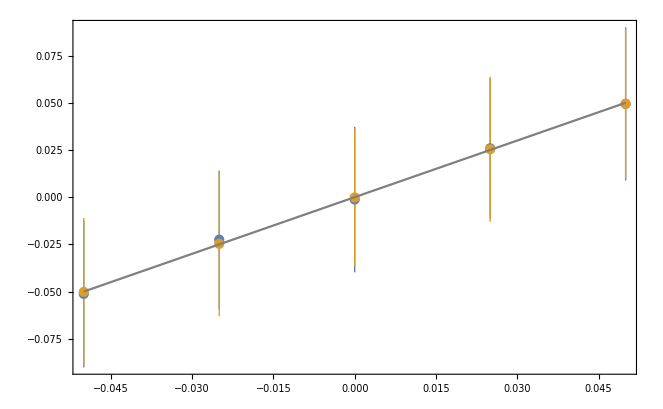

0.00298595

0.00276477

0.002753

0.00280058

0.00315826

```mathematica
SetDirectory[NotebookDirectory[]];

thetasX=Import["thetas_x.csv","CSV"];
thetasY=Import["thetas_y.csv","CSV"];
(* order is θ = -0.05, -0.025, 0, 0.025, 0.05 *)

thetasIdeal=Table[x,{x,-0.05,0.05,0.025}];

meansX=Mean[thetasX]
meansY=Mean[thetasY]
stdX=StandardDeviation[thetasX];
stdY=StandardDeviation[thetasY];

dataX=Range[Length[thetasIdeal]];
dataY=Range[Length[thetasIdeal]];
For[i=1,i≤Length[dataX],i++,
dataX[[i]]={thetasIdeal[[i]],Around[meansX[[i]],stdX[[i]]]};
dataY[[i]]={thetasIdeal[[i]],Around[meansY[[i]],stdY[[i]]]};
]

Show[ListPlot[{dataX,dataY},Frame->True],Plot[x,{x,-0.05,0.05},PlotStyle->Gray]]

MSE1=Mean[(-0.05-thetasX[[All,1]])^2+(-0.05-thetasY[[All,1]])^2]
MSE2=Mean[(-0.025-thetasX[[All,2]])^2+(-0.025-thetasY[[All,2]])^2]
MSE3=Mean[(0-thetasX[[All,3]])^2+(0-thetasY[[All,3]])^2]
MSE4=Mean[(0.025-thetasX[[All,4]])^2+(0.025-thetasY[[All,4]])^2]
MSE5=Mean[(0.05-thetasX[[All,5]])^2+(0.05-thetasY[[All,5]])^2]
```

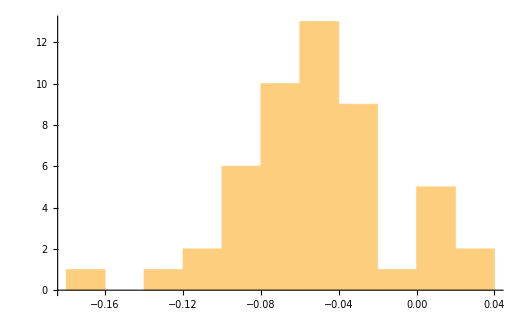

```mathematica
Histogram[thetasX[[All,1]],10]
```

(-0.00305844
0.000369185
-0.0028513
-0.000895832
-0.0070391
-0.0117497
0.00982979
-0.027352
-0.0786061)

(0.00285281
0.0096651
0.00524612
0.00303156
-0.00691684
-0.00970634
0.00738736
0.00730651
0.00205642)

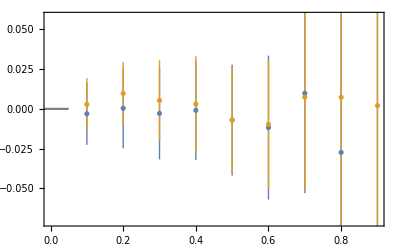

0.1 | 0.000602816 | 0.000659169
0.2 | 0.000762939 | 0.00109908
0.3 | 0.000996492 | 0.00148157
0.4 | 0.00135634 | 0.00185651
0.5 | 0.00195313 | 0.00240129
0.6 | 0.00305176 | 0.00387154
0.7 | 0.00542535 | 0.00733079
0.8 | 0.012207 | 0.0234846
0.9 | 0.0488281 | 0.126815

```mathematica
thetasXϵ=Import["thetas_x_eps.csv","CSV"];
thetasYϵ=Import["thetas_y_eps.csv","CSV"];
(* order is ϵ = 0.1, ... , 0.9 *)

ϵIdeal=Table[x,{x,0.1,0.9,0.1}];

meansXϵ=Mean[thetasXϵ]
meansYϵ=Mean[thetasYϵ]
stdXϵ=StandardDeviation[thetasXϵ];
stdYϵ=StandardDeviation[thetasYϵ];

dataXϵ=Range[Length[ϵIdeal]];
dataYϵ=Range[Length[ϵIdeal]];
For[i=1,i≤Length[dataXϵ],i++,
dataXϵ[[i]]={ϵIdeal[[i]],Around[meansXϵ[[i]],stdXϵ[[i]]]};
dataYϵ[[i]]={ϵIdeal[[i]],Around[meansYϵ[[i]],stdYϵ[[i]]]};
]

Show[ListPlot[{dataXϵ,dataYϵ},Frame->True],Plot[0,{x,-0.05,0.05},PlotStyle->Gray]]

MSEs={Mean[Abs[thetasXϵ[[All,1]]]^2+Abs[thetasYϵ[[All,1]]]^2],Mean[Abs[thetasXϵ[[All,2]]]^2+Abs[thetasYϵ[[All,2]]]^2],Mean[Abs[thetasXϵ[[All,3]]]^2+Abs[thetasYϵ[[All,3]]]^2],Mean[Abs[thetasXϵ[[All,4]]]^2+Abs[thetasYϵ[[All,4]]]^2],Mean[Abs[thetasXϵ[[All,5]]]^2+Abs[thetasYϵ[[All,5]]]^2],Mean[Abs[thetasXϵ[[All,6]]]^2+Abs[thetasYϵ[[All,6]]]^2],Mean[Abs[thetasXϵ[[All,7]]]^2+Abs[thetasYϵ[[All,7]]]^2],Mean[Abs[thetasXϵ[[All,8]]]^2+Abs[thetasYϵ[[All,8]]]^2],Mean[Abs[thetasXϵ[[All,9]]]^2+Abs[thetasYϵ[[All,9]]]^2]};
table=Table[{eps,4/(1-eps)^2/8192},{eps,0.1,0.9,0.1}];
Transpose[{table[[All,1]],table[[All,2]],MSEs}]//TableForm
```

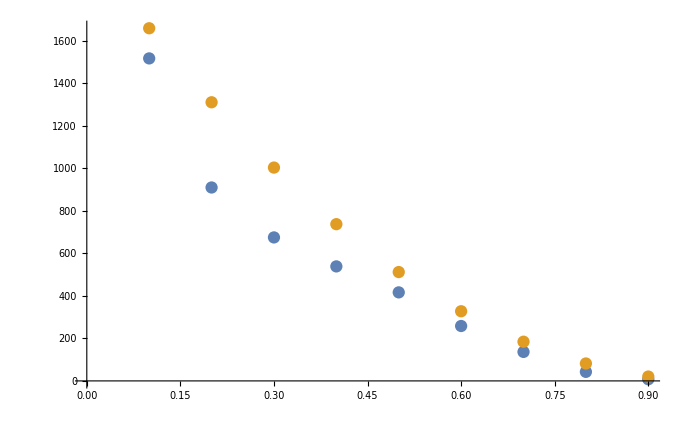

```mathematica
data=Transpose@{table[[All,1]],1/MSEs};
datatheory=Transpose@{table[[All,1]],1/table[[All,2]]};
ListPlot[{data,datatheory}]
```

```mathematica
Mean[Abs[thetasXϵ[[All,5]]]^2]
Mean[Abs[thetasYϵ[[All,5]]]^2]
```

0.00123801

0.00116328